#### Hiring talent and effort : numerical example 2

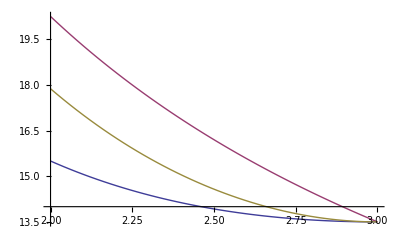

```mathematica
K=27; 
tl=2;
tb=3;
hr[t_]=(3-t); (*(1-F)/f for uniform distribution between 2 and 3*)
gamma=12;(*fixed cost parameter; plays only a role for participation constraint*)
c[q_,t_]=(q^2 t^2-2K q t+K^2)/(t^4)+(3-t) gamma; (*cost function*)
qfb[t_]=(t^2)/2+K/t;(*first best decision where principal's benefit is q minus the transfer payment*)
s[t_]=3K/(2t);(*sign switching decision*)
qr[t_]=(t^4+2K t+6K hr[t])/(2t^2+4t hr[t]);(*relaxed solutuion, i.e. taking only local ic into account*)
Plot[{qfb[t],s[t],qr[t]},{t,2,3}]
```

```mathematica
hreta[t_,n_]=(3-t-n); (*(1-F-eta)/f*)
qeta[t_,n_]=(t^4+2K t+6K hreta[t,n])/(2t^2+4t hreta[t,n]);(*decision with some given eta*)
```

```mathematica
(*This is the algorithm: for qeta the corresponding rents and non-local incentive constraints are calculated*)
```

```mathematica
integrand[x_,n_]=FullSimplify[((2(qeta[x,n])^2 x^2-6K qeta[x,n] x+4K^2)/(x^5)+gamma)];
pieta[t_,n_]=Assuming[{2≤t≤3,0≤n≤12/10},Integrate[integrand[x,n],{x,2,t}]];
Phieta[t_,h_,n_]=pieta[t,n]-pieta[h,n]-c[qeta[h,n],h]+c[qeta[h,n],t];
```

```mathematica
(*Next part of the algorithm: Minimize Phieta and check the minimal value of Phieta*)
```

```mathematica
Sol={Table[N[y/1000,5],{y,0,200,20}],{},{},{}};
Do[OP=NMinimize[{Phieta[t,h,n]/.{n->i/1000},2≤h≤t≤3},{{t,290/100,3},{h,2,210/100}},AccuracyGoal->6,PrecisionGoal->4,WorkingPrecision->40];Sol[[2]]=Append[Sol[[2]],N[OP[[2,1]],5]];Sol[[3]]=Append[Sol[[3]],N[OP[[2,2]],5]];Sol[[4]]=Append[Sol[[4]],N[OP[[1]],6]],{i,0,200,20}]
Sol
```

{{0,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2},{t→3.,t→3.,t→3.,t→3.,t→3.,t→3.,t→3.,t→3.,t→3.,t→3.,t→3.},{h→2.,h→2.,h→2.,h→2.,h→2.,h→2.,h→2.,h→2.,h→2.,h→2.,h→2.},{-0.147472,-0.13247,-0.117201,-0.101656,-0.0858305,-0.0697138,-0.0532984,-0.0365737,-0.0195311,-0.00216057,0.0155481}}

Sol includes 4 lists : 1) the tried eta; 2) the type t minimizing Phieta; 3) the type h minimizing Phieta; 4) the value of Phieta at (t, h)

the results indicate that etabar is between 0.18 and 0.2 as the minimal Phieta changes from negative to positive around there. Let's take 0.19:

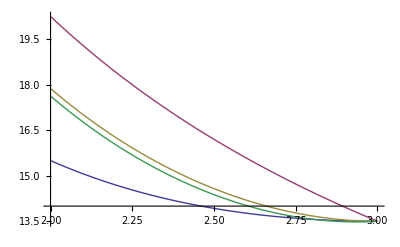

```mathematica
Plot[{qfb[t],s[t],qr[t],qeta[t,0.19]},{t,2,3}]
```

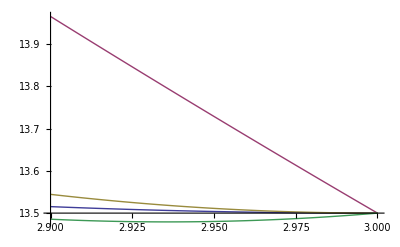

```mathematica
(*zoom to illustrate need for ironing: the obtained solution is not monotone for types around 3*)
Plot[{qfb[t],s[t],qr[t],qeta[t,0.19]},{t,2.9,3}]
```

```mathematica
(*Find the type minimizing qeta, i.e. where the monotonicity of qeta starts to be violated*)
```

```mathematica
Reduce[{D[qeta[t,n], t]==0,2≤t≤3,0≤n≤1/4},t]
```

0≤n≤1/4&&t==Root[1458-972 n+162 n^2+(-486+162 n) #1+54 #1^2+(-9+3 n) #1^4+#1^5&,2]

```mathematica
tmin[n_]=Root[1458-972 n+162 n^2+(-486+162 n) #1+54 #1^2+(-9+3 n) #1^4+#1^5&,2];
```

```mathematica
(*Next, find the ironing interval with the usual ironing condition. Note that the bunching interval has to go up to type 3 as otherwise the monotonicity constraint would still be violated for the highest type(s). *)
fociron[x_,n_]=FullSimplify[Assuming[{2<x<3,0≤n<1/4},∫_x^3 (1-2(qeta[x,n] t-K)/(t^3)+hreta[t,n](-4qeta[x,n] t+6K)/(t^4))ⅆt]]
```

((-3+x)^2 (54 (-3+n)^2+36 (-3+n) n x+18 n x^2+6 (-3+n) x^3+n x^4))/(9 x^3 (-6+2 n+x))

```mathematica
(*Clearly, the ironing interval has to start at a type below tmin[n] to satisfy the usual ironing condition*)
Reduce[{fociron[x,n]==0,2<x<tmin[n],0≤n<1/4},x,Reals]
```

0<n<1/4&&x==Root[486-324 n+54 n^2+(-108 n+36 n^2) #1+18 n #1^2+(-18+6 n) #1^3+n #1^4&,1]

```mathematica
(*plug together the ironed out qeta and rerun the algorithm with these ironed out qeta. *)
```

```mathematica
startiron[n_]=Root[486-324 n+54 n^2+(-108 n+36 n^2) #1+18 n #1^2+(-18+6 n) #1^3+n #1^4&,1];
qetairon[t_,n_]=Piecewise[{{qeta[t,n],t<startiron[n]},{qeta[startiron[n],n],t≥startiron[n]}}];
integrandiron[x_,n_]=FullSimplify[((2(qetairon[x,n])^2 x^2-6K qetairon[x,n] x+4K^2)/(x^5)+gamma)];
pietairon[t_,n_]=Assuming[{2≤t≤3,0≤n≤1},Integrate[integrandiron[x,n],{x,2,t}]];
Phietairon[t_,h_,n_]=pietairon[t,n]-pietairon[h,n]-c[qetairon[h,n],h]+c[qetairon[h,n],t];
```

```mathematica
Save["data_ex_ex2_uni",{startiron,qetairon,pietairon,Phietairon,qeta,hreta,fociron,tmin,qfb,s,K,qr,c,gamma}];
```

In this example, it is clear that the non - local ic can only bind from type 3 to type 2. Hence, we do not have to run the numerical minimization but can simply check Phietairon at those types :

```mathematica
For[i=16,i<21,i++,{Print[i],Print[N[Phietairon[3,2,i/100]],5]}]
```

16

-0.01953525

17

-0.01089285

18

-0.002167385

19

0.006642295

20

0.01553755

```mathematica
startiron[0.18]
```

2.90915

```mathematica
(*zoomed in plot of solution:*)
```

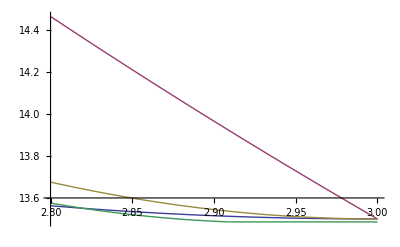

```mathematica
Plot[{qfb[t],s[t],qr[t],qetairon[t,0.18]},{t,2.8,3}]
```

```mathematica
(*quick check that participation constraints are fine:*)
```

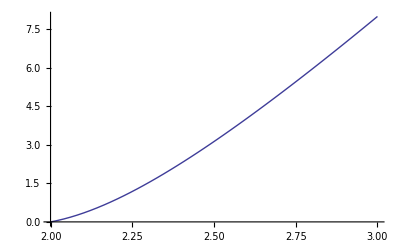

```mathematica
Plot[pietairon[t,0.18],{t,2,3}]
```